## Tahm’s Wolfram Language Cheat Sheet

```mathematica
@ -> another means of applying a function (like Brackets
```

Map---new list by applying a function to each element in the list-----/@ is \
the same as map
MapApply---applies a function to individual parts of the list \
---MapApply[f,{{x,y}},{z},{a,b,c}} ---@@@ is the same as Map Apply---f @@@ \
{{x, y}, {z}, {a, b, c}}
//---Applies a function as an afterthought ---Array[Plus,{10,10}]//Grid 
Circle---[1,1] is the center and x= the radius, Graphics[Table[Circle[{1, 1}, x], {x, 1, 5}]]
GeoDistance---Finds the distance between two geographic places--- 
UnitConvertGeoDistance New York City CITY , London CITY , 
km  ;; 25 volcanoes to Rome\nGeoListPlotGeoNearest
"Volcano", Rome CITY , 25
ListLinePlot---creates a a line plot out of a list
Grid----makes a grid out of things ----Grid[Table[x * y, {x, 12}, {y,
12}]; Grid[Table[RandomColor[], {x, 10}, {y, 10}], Frame → All
Ex. Grid[Array[Times, {5, 5}]]
How Lists Can multiply---Prime[{1,100,10000,10000}]
Functions: --- # is a placeholder for a pure symbol and then &/ is the way to apply 
it: Blur[#,5]&/@{A,B,C}\nEx. Select[Range[100], MemberQ[IntegerDigits[#], 2]
&]
Column---puts things into a column: f[#,{x,#},{#,#}]&/@{a,b,c}//Column
NestList---Nestlist makes a list of the results of nesting f---NestList[f,x,4] 
-----NestList[#+1&,1,15]-- use &, for nest list
Ex. NestList[3*3#&,1,10]
Ex. NestList[Rotate[Framed[#],RandomReal[{0,360}]]&,Style[“A”,50],5]
Ifs-----if statements create either ors If[# < 4, x, y] & /@ {1, 2, 3, 4, 5, 6, 
7}. If[StringLength[#] > 5, Nothing, StringReverse[#]] & /@ 
RandomSample[WordList[], 50
If[First[IntegerDigits[#]]>5,#,Nothing]&/@Array[Prime,100]
Select---Select will filter the list to match certain cases: Select[{1, 2, 3, 4, 5, \
6, 7}, # > 3 &]
Ex. Select[IntegerName[Range[100]],StringTake[#,1]==StringTake[StringReverse[#],1]&]
Ex. Select[Select[WordList[],StringLength[#]==10&],Total[LetterNumber/@Characters[#]]==100&]
FoldList---FoldList[f,x,{1,2,3,4,5}], FoldList[#1 + #2 &, 0, {1, 1, 1, 2, 0, 0}]
Transpose------ Moves its into a set of lists---Transpose[{{1, 2}, {3, 4}, {5, 6},
{7, 8}, {9, 10}}]
Gather------gathers a list into similar elements\nEx. GatherBy[Characters[
"It's true that 2+2 is equal to 4!]
Union--------get the elements within a list \nEx. Union[{1, 9, 5, 3, 1, 4, 3, 1, 3, \
3, 5, 3, 9}]
Intersection------find the elements common to all listsEx. Intersection[{2, 1, 3, 7, 9}, {4, 5, 1, 2, 3, 3}, {3, 1, 2, 8}]
Complement---find the elements that are unique to one another\n Ex. Complement[{4, 5, \
1, 2, 3, 3}, {3, 1, 2, 8}]
Part------ Outputs a part of a list---Part[{a, b, c, d, e, f, g}, 2] same as \
take[[]]
Position---outputs the position of a certain element Ex.Position[Characters["The Wolfram Language”]
positions = Transpose[{xPositions, yPositions}];
ReplacePart----Replaces the part of certain things---ReplacePart[{a, b, c, d, e, f, g}, {3 -> x, 5 -> y}]
IntegerDigits[Range[100]]/.Thread[{0->Red,9->Orange}]
EvenQ--- Gives a true false statement: 
Ex. If[EvenQ[#],Framed[Style[#,Background->Yellow]], Style[#, Background->LightGray]]&/@Range[100]
MatchQ---Provides a true or false outcome for math pairs--- MatchQ[#, {b, _}] & /@ {{a, a}, {b, a}, {a, b, c}, {b, b}, {c, a}, {b, b, b}}
Cases------- Outputs the instances when something similar occurs
Cases[IntegerDigits[Range[100, 500, 55]], {_, 1 | 2, _}]
Cases[{f[1], g[2], f[2], f[6], g[3]}, f[x_] -> x + 10] 
Cases[IntegerDigits[Range[100,999]],{x_,y_,x_}]
Cases[Interpreter["University"][StringJoin["U of ",#]&/@ToUpperCase[Alphabet[]]],_Entity]
Grid---This is a grid that produces a random 10 by 10 grid of \
number with random colors: Grid[Table[Style[RandomInteger[10], 
RandomColor[]], 10, 10]]
Take--- Is a way to take integers from a part of a list: Take[IntegerDigits[2^1000],-5]
Interpreter----AI function to see what something is 
Interpreter["Chemical"][{"C2H4","C2H6","C3H8"}]
Permutation---offers all possible combinations: Cases[Interpreter["University"][StringJoin["U of ",#]&/@ToUpperCase[Alphabet[]]],_Entity] 
Flatten---Flattens the lists in a string
Flatten[Table[WordTranslation[IntegerName[x],"French"],{x,2,10}]] 
CloudPublish---Makes a website: CloudPublish[FormPage[{"String"->"String"},Style[StringReverse[#String],50]&]] 
Module: Create a localized variable , both variables and functions must be in a list
Table[StringJoin[
Module[{x,y},x=Characters["aeiou"];y=Complement[Alphabet[],x];
RandomChoice/@{x,y,x,y,x}]],10]
Module[{x=Table[RandomInteger[100],10]},Column[{x,Sort[x],Max[x],Total[x]}]]
 
Symbols:
&& = and
|| = or
! =  not
;; = range

f[{a,b,c,d,e}]

f[a,b,c,d,e]

{a,b,c,d,e}

{f[a],f[b],f[c],f[d],f[e]}

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

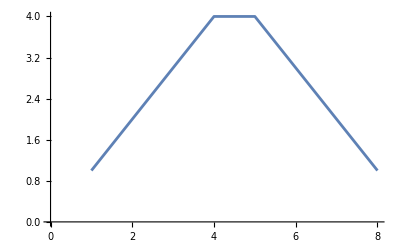

```mathematica
f@{a,b,c,d,e}
f@@{a,b,c,d,e}
f@@@{a,b,c,d,e}
f/@{a,b,c,d,e}


Cubical grid of Masses:

Array[Plus,{10,10}]//Grid
```